# Question 01

```mathematica
r=ⅇ^Cos[t]-2*Cos[4*t]+Sin[t/12]^5
```

ⅇ^Cos[t]-2 Cos[4 t]+Sin[t/12]^5

## (a) Using polar plot

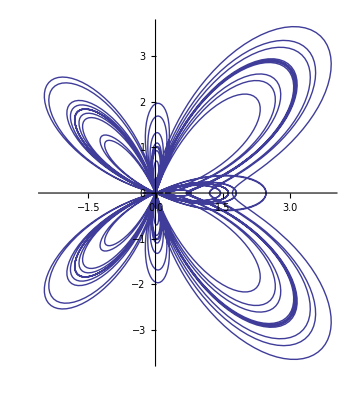

```mathematica
PolarPlot[r,{t,0,24*Pi}]
```

## (b) Using ParametricPlot

```mathematica
ParametricPlot[r{Cos[t],Sin[t]},{t,0,24*Pi}]
```

-Graphics-

# Question 02

```mathematica
f[x_,y_]:=(x^2*y)/(x^4+4*y^2)
```

```mathematica
Plot3D[f[x,y],{x,-30,30},{y,-30,30},Axes->{True, True, True},AxesLabel->{x,y,z},
PlotStyle->Directive[Orange],
PlotPoints->50]
```

-Graphics3D-

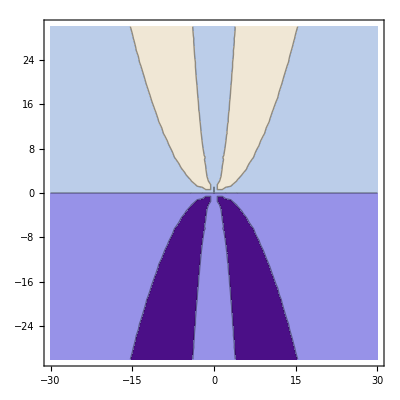

```mathematica
ContourPlot[f[x,y],{x,-30,30},{y,-30,30},Contours-> 3]
```

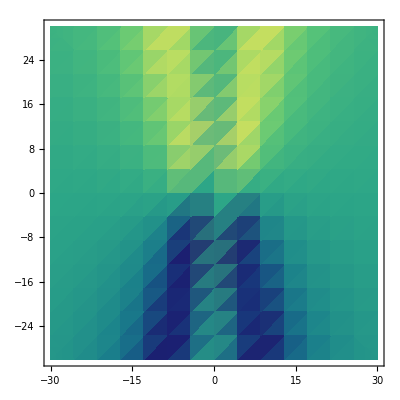

```mathematica
DensityPlot[f[x,y],{x,-30,30},{y,-30,30},ColorFunction->"BlueGreenYellow"]
```

# Question 03

```mathematica
p={-2,1,3};n={3,1,5};r={x,y,z};
Print["The equation of plane is: "]
eq1=(r-p).n==0
eq=Solve[eq1,z]
res=eq[[1,1,2]]
Plot3D[res,{x,-10,10},{y,-10,10},AxesLabel->{x,y,z},PlotStyle->Orange,PlotPoints->200]
```

The equation of plane is:

-1+3 (2+x)+y+5 (-3+z)==0

{{z→1/5 (10-3 x-y)}}

1/5 (10-3 x-y)

-Graphics3D-

# Question 04

ClearAll[“Global`*”]

ClearAll

```mathematica
eq1=x^2/16+y^2/4+z^2==1
```

x^2/16+y^2/4+z^2==1

## (i)ParametricPlot3D

```mathematica
ParametricPlot3D[{4*Cos[t]*Cos[r],2*Cos[t]*Sin[r],Sin[t]},{t,-Pi/2,Pi/2},{r,-Pi,Pi},Axes->Automatic,AxesLabel->{x,y,z}]
```

-Graphics3D-

## (ii) ContourPlot3D

```mathematica
eq1
```

x^2/16+y^2/4+z^2==1

```mathematica
ContourPlot3D[x^2/16+y^2/4+z^2==1,
{x,-4,4},{y,-2,2},{z,-1,1},
BoxRatios->{1,2,4},AxesLabel->{x,y,z},MeshStyle->Green
]
```

-Graphics3D-

# Question 05

```mathematica
f[x_]:=ⅇ^(-(x-2)^2)+ⅇ^(-(x-4)^2)
```

## (i)Plot function

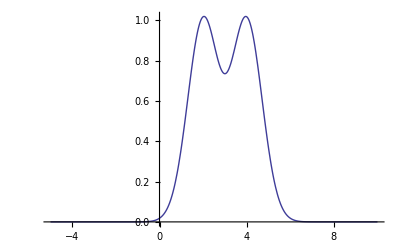

```mathematica
Plot[f[x],{x,-5,10}]
```

## (ii)Volume revolving disc and washer method

```mathematica
vol=Integrate[Pi*f[x]^2,{x,1,5}]//N
```

8.76132

## (iii)X-axis

RevolutionPlot3D

```mathematica
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{1,0,0}]
```

ParametricPlot3D

```mathematica
ParametricPlot3D[{f[x]*Cos[t],f[x]*Sin[t],x},{x,1,5},{t,0,2*Pi},BoxRatios-> Automatic]
```

-Graphics3D-

## (iv)Volume by cylindrical shell method

```mathematica
vol2=∫_1^5 f[x]*2*Pi*xⅆx//N
```

61.5638

## (v)Y-Axis

RevolutionPlot3D

```mathematica
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{0,0,1},AxesLabel->{x,y,z}]
```

-Graphics3D-

ParametricPlot3D

```mathematica
ParametricPlot3D[{x*Cos[t],x*Sin[t],f[x]},{x,1,5
},{t,0,2*Pi},BoxRatios->{4,4,1},AxesLabel->{x,y,z}]
```

-Graphics3D-

# Question 06

```mathematica
z1=4*x^2+4*y^2;
z2=16-4*x^2-4*y^2;
```

```mathematica
g1=ContourPlot3D[z==4*x^2+4*y^2,{x,-2,2},{y,-2,2},{z,0,16}];
g2=ContourPlot3D[z==16-(4*x^2+4*y^2),{x,-2,2},{y,-2,2},{z,0,16}];
Show[g1,g2]
```

-Graphics3D-

```mathematica
vol=Integrate[z2-z1,{x,-1,1},{y,-1,1}]
```

128/3

# Question 07

```mathematica
Remove[x,y,z]
```

```mathematica
z==4-x^2-y^2;
ContourPlot3D[z==4-x^2-y^2,{x,-2,2},{y,-2,2},{z,0,4},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Mesh->None,Boxed->False]
```

-Graphics3D-

```mathematica
vol=Integrate[r*(4-r^2),{t,0,2*Pi},{r,0,2}]
```

8 π

# Question 08

```mathematica
g1=ContourPlot3D[z==1-x-y,{x,0,1},{y,0,1},{z,0,1}];g2=ContourPlot3D[z==1+x+y,{x,0,1},{y,0,1},{z,0,1}];g3=ContourPlot3D[y==1-x,{x,0,1},{y,0,1},{z,0,1}];
g4=ContourPlot3D[y==0,{x,0,1},{y,0,1},{z,0,1}];
g5=ContourPlot3D[x==0,{x,0,1},{y,0,1},{z,0,1}];
g6=ContourPlot3D[z==1,{x,0,1},{y,0,1},{z,0,1}];
g7=ContourPlot3D[z==0,{x,0,1},{y,0,1},{z,0,1}];
Show[g1,g2,g3,g4,g5,g6,g7]
```

-Graphics3D-

```mathematica
rho=(1+x^2+y^2);
dV=Abs[1+x+y-(1-x-y)];
mass=Integrate[rho*dV,{x,0,1},{y,0,1-x}]
```

14/15

# Question 09

```mathematica
f[x_,y_]:=4/(x^2+y^2+1)
x0=1/2;y0=1;
```

```mathematica
s1=D[f[x,y],x]/.{x->x0,y->y0};
s2=D[f[x,y],y]/.{x->x0,y->y0};
s3=-1;
r={s1,s2,s3};
X={x,y,z};
X0={x0,y0,f[x0,y0]};
```

```mathematica
tangent=Solve[r.(X-X0)==0,z][[1,1,2]]
```

-16/81 (-19+4 x+8 y)

```mathematica
normal=Solve[X-X0==r*t,{x,y,z}]//Flatten
```

{x→1/162 (81-128 t),y→1/81 (81-128 t),z→1/9 (16-9 t)}

```mathematica
g1=Plot3D[f[x,y],{x,-2,2},{y,-2,2},Mesh->None];
g2=Plot3D[tangent,{x,-2,2},{y,-2,2},Mesh->None];
g3=ParametricPlot3D[Table[normal[[i,2]],{i,1,3}],{t,-1,1},PlotStyle->{RGBColor[0,1,0],Thickness[.2]}];
(*g4=PlotPoints[Point[X0]]*)
Show[g1,g2,g3,Graphics3D[{Red,PointSize[.1],Point[X0]}]]
```

-Graphics3D-

# Question 10

```mathematica
LessPrimes[n_]:=Module[
{a=n,p={}},
For[i=1,i≤a,i++,
If[PrimeQ[i],p=Append[p,i]]
]
;p
]
LessP=LessPrimes[50]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47}